0.516949 x[t]+1.24 x'[t]+x''[t]==0

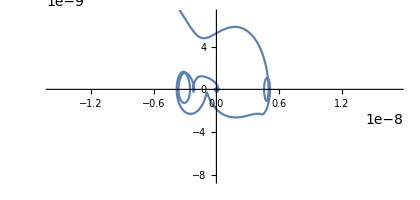

```mathematica
δ=.62;
Subscript[ω, 0]=30.5/59;

eq=x''[ t ]+2 δ x'[ t ]+Subscript[ω, 0] x [ t ] == 0

wp1 = x [0] == 1;
wp2 = x'[0] == 1;
sol=NDSolve [ { eq, wp1, wp2 }, x, {t , 0, 100}];
ParametricPlot [ Evaluate [{ x [ t ], x'[ t ]}/.sol], {t , 0, 100}]
```